C[1] Cos[t]+C[2] Sin[t]

Cos[t]

-Sin[t]

-Cos[t]

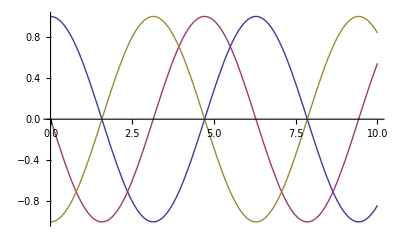

```mathematica
(*Solve the boundary value differntial equation :x''[t]+w^2x[t]=0,where boundary conditions are x[0]=1,x[T/4]=0,T=2pi/w*)
(*Solution*)
w=1;T=2 Pi/w;
deq=x''[t]+w^2x[t]==0;
xt=DSolve[deq,x[t],t];
xt=x[t]/.xt[[1]]
aeq1=(xt/.t->0)==1;
aeq2=(xt/.t->T/4)==0;
const=Solve[{aeq1,aeq2},{C[1],C[2]}];
xt=xt/.const[[1]]
vt=D[xt,t]
at=D[xt,{t,2}]
Plot[{xt,vt,at},{t,0,10}]
```

```mathematica
w=1;T=2 Pi/w;
deq=x''[t]+w^2x[t]==0;
sol=DSolve[{deq,x[0]==1,x[T/4]==0},x,t]
DSolve[{deq,x[0]==1,x[T/4]==0},x[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument x[t] + SuperscriptBox[Truex[π/2] == 0.

DSolve[{x[t]+x''[t]==0,True,x[π/2]==0},x,t]

DSolve::deqn: Equation or list of equations expected instead of True in the first argument x[t] + SuperscriptBox[Truex[π/2] == 0.

DSolve[{x[t]+x''[t]==0,True,x[π/2]==0},x[t],t]

```mathematica
?DSolve
```

DSolve[eqn,y,x] solves a differential equation for the function y, with independent variable x. 
DSolve[{eqn_1,eqn_2,…},{y_1,y_2,…},x] solves a list of differential equations. 
DSolve[eqn,y,{x_1,x_2,…}] solves a partial differential equation.